Problem 4a
Find the associated vorticity for the stream function given. Show that on the set of Reals in 2D, the integral of the vorticity is =1 for all values of delta.

```mathematica
Psi[x_,y_,δ_] :=-1/(2*Pi)*Log[(x^2+y^2+δ^2)^(1/2)]
ω[x_,y_,δ_] =  -Laplacian[Psi[x,y,δ],{x,y}] // Simplify
```

δ^2/(π (x^2+y^2+δ^2)^2)

```mathematica
Integrate[ω[x,y,δ],{x,-∞,∞},{y,-∞,∞}] // Simplify
```

ConditionalExpression[1,Re[δ^2]≥0||δ^2∉Reals]

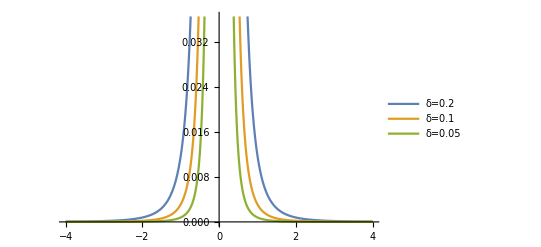

```mathematica
Plot[{ω[x,0,0.2],ω[x,0,0.1],ω[x,0,0.05]},{x,-4,4},PlotRange->Automatic, PlotLegends->{"δ=0.2","δ=0.1","δ=0.05"}]
```